```mathematica
Expand[(4+4z+3z^2)^2+16z^2]
```

16+32 z+56 z^2+24 z^3+9 z^4

```mathematica
AA[x_,y_]:=(4+4(x+I y)+3(x+I y)^2)
BB[x_,y_] :=Sqrt[9(x+I y)^4+24(x+I y)^3+56(x+I y)^2+32(x+I y)+16]
```

```mathematica
eqn[x_,y_]:=Max[
Abs[(AA[x,y]- BB[x,y])/8],
Abs[(AA[x,y]+BB[x,y])/8]]
```

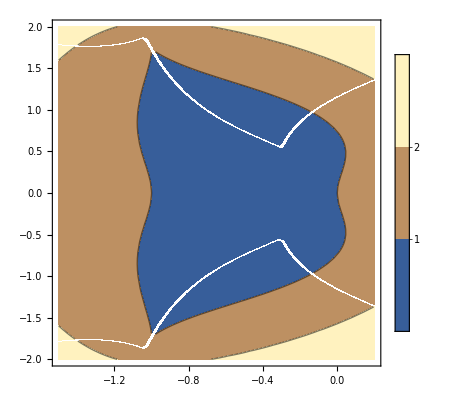

```mathematica
ContourPlot[eqn[x,y],{x,-1.5,0.2},{y,-2,2},PlotLegends->BarLegend[Automatic,All],Contours->{-1,0,1,2}]
```